#### Kamen setup

```mathematica
kamen[x_]:=0.96-0.25(x-0.5)^2
FindRoot[kamen[x],{x,-2}]
```

{x→-1.45959}

```mathematica
{x->-1.4595917942265424}
```

```mathematica
{x->2.4595917942265424}
```

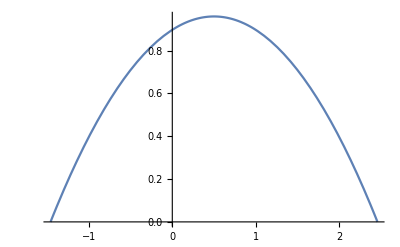

```mathematica
kamenPlot=Plot[kamen[x],{x,-1.4595917942265424,2.4595917942265424}]
```

#### String setup

```mathematica
k=1;
g=-1;
boundaryHeightLeft=0.8;
boundaryHeightRight=1.2;
boundaryLeft =-1;
boundaryRight=2;
nXPoints=100;(* Tu klameme, nepocitame totiz bod v "boudaryLeft". Takze oficialne este je o jeden bod naviac. *)

(* Finite difference method - rozdelime x-ovu os na bodiky, v tychto bodoch pocitame "y" *)
dx=(boundaryRight-boundaryLeft)/nXPoints;
xPoints = Table[boundaryLeft+dx*i,{i,0,nXPoints}];
```

Toto navadza na sustavu rovnic -> matica*y=hodnoty, kde pozname maticu a hodnoty: (vid text)

```mathematica
(* Opisanie matice a vektora podla textu *)
matica = 1/dx^2* Table[If[i==j,2, If[Abs[i-j]==1,-1,0]],{i,0,nXPoints},{j,0,nXPoints}];
hodnoty = Table[-1+If[i==0 || i==nXPoints,1/dx^2,0],{i,0,nXPoints}];

(* Sustavu treba vyriesit. Kedze je to ilustracne, tak pouzivam LinearSolve, ale inak by sme to mali robit prave asi tym Newtonom, alebo ako. *)
ypsilony = LinearSolve[matica,hodnoty];
```

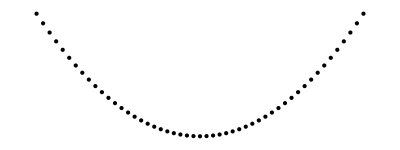

```mathematica
(* Transpose[{xPoints,ypsilony}]; *)
(* Previsnute body bez väzieb. *)
body = Graphics[Point[Transpose[{xPoints,ypsilony}]]]
```

#### Praca s kamenom a String-om - funguje tu zatial iba ten PLOT, kam by sme mohli hodit vsetky veci dokopy.

```mathematica
psi[y_]:=1/2*k*(D[y,x])^2-g*y;
potential[y_]:=Integrate[psi[y],{x,0,1}];
psi[y[x]];
potential[y[x]];
```

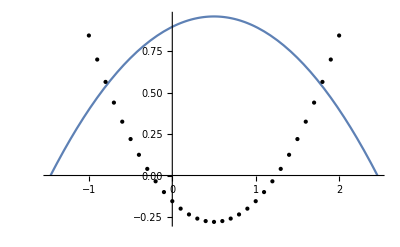

```mathematica
Show[kamenPlot, body, PlotRange->All]
```

```mathematica
ycords=Table[Subscript[y,i],{i,1,nXPoints-1}];
lambdas = Table[Subscript[λ,i],{i,1,nXPoints-1}];
ρ=10;
functions2[list_]:=Table[(-list[[i-1]]+2*list[[i]]-list[[i+1]])/dx^2+ 1+Piecewise[{{list[[nXPoints-1+i]]+ρ*(list[[i]]-kamen[xPoints[[i+1]]]),list[[nXPoints-1+i]]+ρ*(list[[i]]-kamen[xPoints[[i+1]]])<=0},{0,list[[nXPoints-1+i]]+ρ*(list[[i]]-kamen[xPoints[[i+1]]])>0}}],{i,2,nXPoints-2}];
functions4[list_]:=Table[Piecewise[{{(list[[i]]-kamen[xPoints[[i+1]]]),list[[nXPoints-1+i]]+ρ*(list[[i]]-kamen[xPoints[[i+1]]])<=0},{-list[[nXPoints-1+i]]/ρ,list[[nXPoints-1+i]]+ρ*(list[[i]]-kamen[xPoints[[i+1]]])>0}}],{i,1,nXPoints-1}];
functions1[list_]:={(-boundaryHeightLeft+2*list[[1]]-list[[2]])/dx^2+ 1+Piecewise[{{list[[nXPoints]]+ρ*(list[[1]]-kamen[xPoints[[2]]]),list[[nXPoints]]+ρ*(list[[1]]-kamen[xPoints[[2]]])<=0},{0,list[[nXPoints]]+ρ*(list[[1]]-kamen[xPoints[[2]]])>0}}]}
functions3[list_]:={(-list[[nXPoints-2]]+2*list[[nXPoints-1]]-boundaryHeightRight)/dx^2+ 1+Piecewise[{{list[[2*nXPoints-2]]+ρ*(list[[nXPoints-1]]-kamen[xPoints[[nXPoints]]]),list[[2*nXPoints-2]]+ρ*(list[[nXPoints-1]]-kamen[xPoints[[nXPoints]]])<=0},{0,list[[2*nXPoints-2]]+ρ*(list[[nXPoints-1]]-kamen[xPoints[[nXPoints]]])>0}}]}
J[x_]:=D[Join[functions1[Join[ycords, lambdas]],functions2[Join[ycords, lambdas]],functions3[Join[ycords, lambdas]],functions4[Join[ycords, lambdas]]],{Join[ycords, lambdas]}]/.Table[Rule[Join[ycords, lambdas][[i]],x[[i]]],{i,1,2*nXPoints-2}]
Newton[x0_]:=NestWhile[LinearSolve[J[#],-Join[functions1[#],functions2[#],functions3[#],functions4[#]]]+#&,x0,Norm[#]>0.000001&,1,30]
```

```mathematica
sol=Newton[Table[0.5,{i,1,2*nXPoints-2}]]
```

{0.410035,0.420469,0.431304,0.442539,0.454174,0.466208,0.478643,0.491478,0.504713,0.518347,0.532382,0.546817,0.561652,0.576886,0.592521,0.608556,0.624991,0.641825,0.65906,0.676695,0.69473,0.711956,0.720694,0.721787,0.716049,0.706249,0.696849,0.687849,0.679249,0.671049,0.663249,0.655849,0.648849,0.642249,0.636049,0.630249,0.624849,0.619849,0.615249,0.611049,0.607249,0.603849,0.600849,0.598249,0.596049,0.594249,0.592849,0.591849,0.591249,0.591049,0.591249,0.591849,0.592849,0.594249,0.596049,0.598249,0.600849,0.603849,0.607249,0.611049,0.615249,0.619849,0.624849,0.630249,0.636049,0.642249,0.648849,0.655849,0.663249,0.671049,0.679249,0.687849,0.696849,0.706249,0.716049,0.721787,0.720694,0.711956,0.69473,0.676695,0.65906,0.641825,0.624991,0.608556,0.592521,0.576886,0.561652,0.546817,0.532382,0.518347,0.504713,0.491478,0.478643,0.466208,0.454174,0.442539,0.431304,0.420469,0.410035,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-3.0202,-22.2231,-20.1111,-18.0759,-11.1565,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-11.1565,-18.0759,-20.1111,-22.2231,-3.0202,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

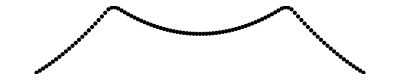

```mathematica
bodyy=Transpose[{xPoints,Join[{boundaryHeightLeft},sol[[;;nXPoints-1]],{boundaryHeightRight}]}];
body2 = Graphics[Point[bodyy]]
```

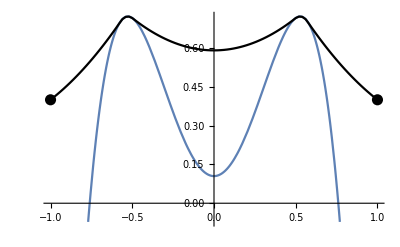

```mathematica
Show[kamenPlot, ListLinePlot[bodyy,PlotStyle->Black],Graphics[{PointSize[0.02],Point[{{boundaryLeft,boundaryHeightLeft},{boundaryRight,boundaryHeightRight}}]}], PlotRange->All]
```

```mathematica
(*Jej supr, vypadá to, že jen nekopíruje tu parabolu, takže to asi něco počítá :D*)
(*Funguje to dobře i pro různé hodnoty parametrů nXPoints a Boundary*)
```

```mathematica
kamen[x_]:=0.5-8*(x-1/3)*(x-2/3)*(x+1/3)*(x+2/3)
kamenPlot=Plot[kamen[x],{x,-0.77,0.77}];
boundaryHeightLeft=0.4;
boundaryHeightRight=0.4;
boundaryLeft =-1;
boundaryRight=1;
nXPoints=100;
dx=(boundaryRight-boundaryLeft)/nXPoints;
xPoints = Table[boundaryLeft+dx*i,{i,0,nXPoints}];
```